## Plot Equilibria of the seasonal Ricker model

### Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
raw=Import["data_export/equi_data/equi_data1.csv"];
```

### Parameter Plane over rb and rnb

```mathematica
(* Plot of non-breeding equilibrium *)
equiDataNB=raw[[2;;,{2,3,4}]];
```

```mathematica
(* Points where oscillations occur *)
oscillPts=Cases[equiDataX,{_,_,"Period-2 oscillations"}];
(* Points where extinction occurs *)
extPts=Cases[equiDataX,{_,_,0}];
extPos=Flatten[Position[equiDataX,#]&/@extPts,1];
```

```mathematica
(* Delete points *)
equiDataX2=Delete[equiDataX,posDel];
```

```mathematica
(* Max and min value *)
valMax=Max[equiDataX[[;;,3]]][[1]];
```

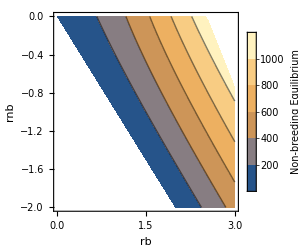

```mathematica
(* Contour plot *)
plotEquiNB=ListContourPlot[equiDataNB,
InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{1,All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding \nEquilibrium",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
(*RegionFunction->(#2<f[#1]&)*)]
```

```mathematica
(* Plot of breeding equilibrium *)
equiDataB=raw[[2;;,{2,3,5}]];
```

```mathematica
(* Max and min value *)
valMax=Max[equiDataB[[;;,3]]][[1]];
```

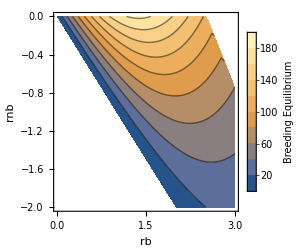

```mathematica
plotEquiB=ListContourPlot[equiDataB,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-2,0},{1,valMax}},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding \nEquilibrium",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```